```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* First we set the physical constants and the rescaled (units-free) quantities *)
ClearAll[g,l,m,energy,Lz,ω0,ξ,λz,α]
g=981/100;l=1;m=1;Lz=2/10;
energy=15;
ω0=N[√(g/l),40] ;
ξ=N[energy/(m*g*l),40] ;
λz=N[Lz^2/(2*m^2*g*l^3),40] ;
α =1/(√(2*ω0^2))*Lz/(m*l^2);

ClearAll[g2,g3]
{g2,g3} = N[{1/4(1+(ξ-1)^2/3),1/16(λz+(2(ξ-1)^3)/27-(2*(ξ-1))/3)},40];
Print[Style["Weierstrass invariants: {g2,g3} =",Red],{g2,g3}]
```

Weierstrass invariants: {g2,g3} ={0.2733246671467359961594453640577704208712,-0.0212308584070021530180795025514790549081}

```mathematica
(* Initial Conditions *)
ClearAll[θ0,ϕ0,vθ0,vϕ0,t0,tmax, sign]

θ0=π/2+π/6 ;ϕ0=π/2 ;

t0=0 ;tmax = 6 ; (* Time interval for plots / numerical integration. *)

sign = -1 ; (* sign can either be +1 or -1, this is the direction fo the \theta velocity. *) 

vϕ0=N[Lz/(m*l^2)*1/Sin[θ0]^2,40]
vθ0=N[sign*√(2*energy/(m*l^2)-Lz^2/(m^2*l^4*Sin[θ0]^2)-2*g/l*(1-Cos[θ0])),40]
```

0.2666666666666666666666666666666666666667

-0.7187952884282608224911313933000394919228

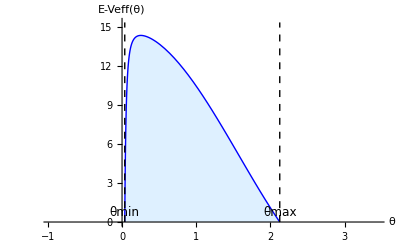

-Graphics-

Motion is restrict to (θmin, θmax) = {0.0365309,2.12496}

```mathematica
(* Setting the possible bound for orbits *)
ClearAll[Veff,Kθ,turningPoints,θmin,θmax,maxVal,minVal,domain,allowedregion,labels,limits,veffplot]

Veff[θ_]:=Lz^2/(2*m*l^2*Sin[θ]^2)+m*g*l*(1-Cos[θ]);
Kθ[θ_]:=energy-Veff[θ]; (* Energy conservation relation *)
turningPoints=θ/. Solve[{Kθ[θ]==0,0<θ<π},θ,Reals];

θmin=Min[turningPoints] ;
θmax=Max[turningPoints] ;

maxVal=NMaxValue[{Kθ[θ],0<θ<π},θ];
minVal=NMinValue[{Veff[θ],0<θ<π},θ];

labels=Graphics[{Text[Style["θmin",12],{θmin,0.05 maxVal},{1.1,0}],Text[Style["θmax",12],{θmax,0.05 maxVal},{-1.1,0}]}];
limits=Graphics[{Dashed,Black,Line[{{θmin,0},{θmin,maxVal+1}}],Line[{{θmax,0},{θmax,maxVal+1}}]}];


domain=Show[Plot[{energy-Veff[θ]},{θ,0,π},PlotStyle->{Blue,Thick},
						Filling->{1->{Axis,LightBlue}},AxesLabel->{"θ","E-Veff(θ)"},
						PlotRange->{{θmin-1,π+.3},{0,maxVal +1}}],
			labels,limits]

allowedregion=RegionPlot[y<=energy&&y>=Veff[θ],{θ,0,π},{y,minVal-0.1,energy+0.1},PlotStyle->LightRed,BoundaryStyle->None];

veffplot=Show[allowedregion,Plot[{Veff[θ],Callout[energy,"Energy",{2.5,energy}]},{θ,0,π},PlotStyle->{Blue,{Red,Dashed}}],
				Frame->False,Axes->True,AxesLabel->{"θ",None},PlotRange->{{0,π+0.3},{minVal-.5,energy+energy/6}}]

Print[Style["Motion is restrict to (θmin, θmax) = ",Red],N[{θmin,θmax}]]
```

```mathematica
(* Here we do a numerical integration of the equations of motion. *)
ClearAll[lagrangean,eomθ,eomϕ,sol,ICs,θ,ϕ]
lagrangean = (m*l^2)/2(θ'[t]^2+Sin[θ[t]]^2*ϕ'[t]^2)-m*g*l*(1-Cos[θ[t]]);
eomθ=D[D[lagrangean,θ'[t]],t] - D[lagrangean,θ[t]] ;
eomϕ=D[D[lagrangean,ϕ'[t]],t] - D[lagrangean,ϕ[t]] ;

ICs=N[{θ[0]==θ0,θ'[0]==vθ0,ϕ[0]==ϕ0,ϕ'[0]==vϕ0},40]

sol=Flatten[NDSolve[{eomθ==0,eomϕ==0,ICs},{θ,ϕ},{t,t0,tmax}]]

ClearAll[numθplot,numϕplot]
numθplot = Plot[Evaluate[θ[t]/.sol],{t,t0,tmax},PlotStyle->{Red,Dashed},PlotRange->All] ;
numϕplot = Plot[Evaluate[ϕ[t]/.sol],{t,t0,tmax},PlotStyle->{Red,Dashed},PlotRange->All] ;
```

{θ[0]==2.094395102393195492308428922186335256131,θ'[0]==-0.7187952884282608224911313933000394919228,ϕ[0]==1.570796326794896619231321691639751442099,ϕ'[0]==0.2666666666666666666666666666666666666667}

{θ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}

```mathematica
(* Exact θ-motion *)
ClearAll[v0, u0,u,theta,exactθplot]

v0 = -1/4(Cos[θ0]+(ξ-1)/3) ;
u0 =  √(2 ω0^2)*t0  - sign*InverseWeierstrassP[v0,{g2,g3}];

u[t_]:=Re[-4*WeierstrassP[(√(2*ω0^2)*t-u0),{g2,g3}]-(ξ-1)/3]//Chop

theta[t_] = ArcCos[u[t]] ;

exactθplot=Plot[{theta[t],Callout[θmin,"θmin",{π,θmin}],Callout[θmax,"θmax",{π,θmax}]},{t,t0,tmax},PlotStyle->{{},{Black,Dashed},{Black,Dashed}},
				AxesLabel->{"t","θ(t)"},PlotRange->{θmin-.3,θmax+.3}]
```

-Graphics-

```mathematica
(* ϕ-motion *)
```

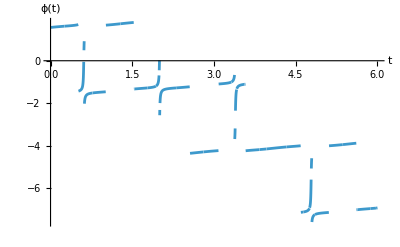

```mathematica
ClearAll[w1,w2,v1,v2,y1,y2,phi1,phi2,exactphi,exactϕplot]

{w1,w2}=N[WeierstrassHalfPeriods[{g2,g3}],40];

v1 =-(ξ+2)/12 ;
v2 =(4-ξ)/12 ; 
y1=InverseWeierstrassP[v1,{g2,g3}];
y2=InverseWeierstrassP[v2,{g2,g3}];

phi1[t_]:=1/WeierstrassPPrime[y1,{g2,g3}]*(2*WeierstrassZeta[y1,{g2,g3}]*√(2 ω0^2)(t-t0)+Log[(WeierstrassSigma[√(2 ω0^2)t-u0-y1,{g2,g3}]*WeierstrassSigma[√(2 ω0^2)t0-u0+y1,{g2,g3}])/(WeierstrassSigma[√(2 ω0^2)t-u0+y1,{g2,g3}]*WeierstrassSigma[√(2 ω0^2)t0-u0-y1,{g2,g3}])])
phi2[t_]:=1/WeierstrassPPrime[y2,{g2,g3}]*(2*WeierstrassZeta[y2,{g2,g3}]*√(2 ω0^2)(t-t0)+Log[(WeierstrassSigma[√(2 ω0^2)t-u0-y2,{g2,g3}]*WeierstrassSigma[√(2 ω0^2)t0-u0+y2,{g2,g3}])/(WeierstrassSigma[√(2 ω0^2)t-u0+y2,{g2,g3}]*WeierstrassSigma[√(2 ω0^2)t0-u0-y2,{g2,g3}])])


exactphi[t_]:=ϕ0+α/8(phi1[t]-phi2[t])//Re

exactϕplot=Plot[exactphi[t],{t,t0,tmax},AxesLabel->{"t","ϕ(t)"}]
```

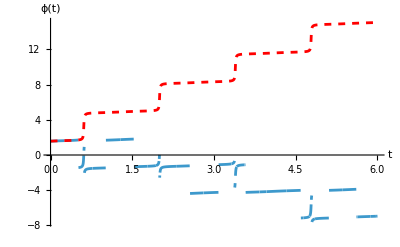

```mathematica
Show[exactϕplot,numϕplot,PlotRange->All]
```

```mathematica
(* Well, at this point we need to discuss the problem with this impleementation. There is no problem at all with the final expression we had obtained for ϕ(t). However, it is likely that the plot of ϕ(t) may not look continous, as it shoud be. The real problem is that "Log" is a multi valued function, and to properly plot the analytical expression we had for the elliptic integral of the third kind it would be required the function to choose the proper branch of the function. A test to verify that, is to just see that different parts obtained from the above plot will be in good agreement by doing ϕ(t) -> ϕ(t) + k*π. *)
```

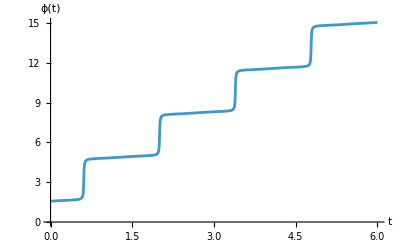

```mathematica
ClearAll[phi,exactϕint]

phi[t_?NumericQ]:=Module[{x0,x1},
						x0=√(2 ω0^2) t0-u0;
						x1=√(2 ω0^2) t-u0;
Re[ϕ0+α/8*NIntegrate[1/(WeierstrassP[x,{g2,g3}]-v1)-1/(WeierstrassP[x,{g2,g3}]-v2),{x,x0,x1},
					WorkingPrecision->MachinePrecision,AccuracyGoal->10,PrecisionGoal->10]]]


exactϕint=Plot[phi[t],{t,t0,tmax},AxesLabel->{"t","ϕ(t)"}]
```

-Graphics-

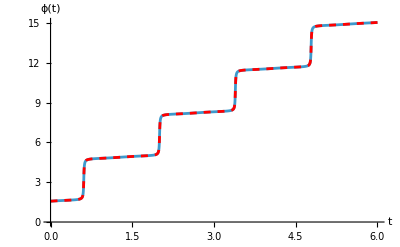

```mathematica
Show[exactθplot,numθplot]
Show[exactϕint,numϕplot]
```

```mathematica
sphere = Graphics3D[{Opacity[0.1],Red,Sphere[{0,0,0},l]}];
```

```mathematica
(* Animation, just for fun *)
ClearAll[x,y,z,orbit]
x[t_?NumericQ]:=l*Sin[theta[t]]*Cos[phi[t]]//Chop
y[t_?NumericQ]:=l*Sin[theta[t]]*Sin[phi[t]]//Chop
z[t_?NumericQ] := -l*Cos[theta[t]]//Chop
orbit = ParametricPlot3D[Re[{x[t],y[t],z[t]}],{t,t0,tmax},AxesLabel->{"x","y","z"}];
```

```mathematica
Show[orbit,sphere,PlotRange->All,ViewPoint->Front]
```

-Graphics3D-

```mathematica
(* Next step is to animate the motion. The easiest way would be to use the numerical solution, which was already tested and produces the same final output as the analytical approach. However, we are not taking that approach, instead let's built everything from our analytical(ish) functions. Note, however, that for larger tmax values this can be quite long proccess. 

To make the animation working properly one needs to first create the data instead of making Mathematica calculate within the animation enviroment. *)

ClearAll[trajdata,trajindex,trajanimated,rod,bob]

trajdata=Table[{x[t],y[t],z[t]},{t,t0,tmax,(tmax-t0)/300}];

trajindex[t_]:=Clip[Round[(t-t0)/(tmax-t0) (Length[trajdata]-1)]+1,{1,Length[trajdata]}];

(* Creating the trajajectory from the data. *)
trajanimated[t_?NumericQ]:=Graphics3D[{Blue,Thick,Line[trajdata[[;;trajindex[t]]]]}];

(* Creating the rod *)
rod[t_?NumericQ]:=Graphics3D[{Black,Line[{{0,0,0},trajdata[[trajindex[t]]]}]}];

bob[t_?NumericQ]:=Graphics3D[{Red,Sphere[trajdata[[trajindex[t]]],0.05 l]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00107531+2.37385 ⅈ}. NIntegrate obtained 596.555-5.19545×10^-13 ⅈ and 8.11078×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00349904+2.37385 ⅈ}. NIntegrate obtained 597.398+1.06546×10^-12 ⅈ and 9.76787×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Animate[Show[sphere,trajanimated[t],rod[t],bob[t],PlotRange->{{-l,l},{-l,l},{-l,l}},AxesLabel->{"x","y","z"},Boxed->False,Axes->True,ViewPoint->Front],{t,t0,tmax},AnimationRate->0.5]
```

```mathematica
(* =============================*)(*Numerical animation (robust)*)(* =============================*)ClearAll[thetaNum,phiNum,xNum,yNum,zNum,trajdataNum,trajindexNum,trajanimatedNum,rodNum,bobNum,frameNum,framesNum]

(*Extract numerical solutions*)
thetaNum[t_?NumericQ]:=Evaluate[θ[t]/. sol]
phiNum[t_?NumericQ]:=Evaluate[ϕ[t]/. sol]

(*Cartesian coordinates*)
xNum[t_?NumericQ]:=l*Sin[thetaNum[t]]*Cos[phiNum[t]]
yNum[t_?NumericQ]:=l*Sin[thetaNum[t]]*Sin[phiNum[t]]
zNum[t_?NumericQ]:=-l*Cos[thetaNum[t]]

(*Precompute trajectory*)
trajdataNum=Table[{xNum[t],yNum[t],zNum[t]},{t,t0,tmax,(tmax-t0)/300}];

trajindexNum[t_]:=Clip[Round[(t-t0)/(tmax-t0) (Length[trajdataNum]-1)]+1,{1,Length[trajdataNum]}];

(*Animated trajectory*)
trajanimatedNum[t_?NumericQ]:=Graphics3D[{Blue,Thick,Line[trajdataNum[[;;trajindexNum[t]]]]}];

(*Rod*)
rodNum[t_?NumericQ]:=Graphics3D[{Black,Line[{{0,0,0},trajdataNum[[trajindexNum[t]]]}]}];

(*Bob*)
bobNum[t_?NumericQ]:=Graphics3D[{Red,Sphere[trajdataNum[[trajindexNum[t]]],0.05 l]}];

(*Frame*)
frameNum[t_?NumericQ]:=Show[sphere,trajanimatedNum[t],rodNum[t],bobNum[t],PlotRange->{{-l,l},{-l,l},{-l,l}},Boxed->False,ViewPoint->Front,ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},SphericalRegion->True,ImageSize->400]

(*Generate frames*)
framesNum=Table[frameNum[t],{t,t0,tmax,(tmax-t0)/200}];

(*Export*)
 Export["spherical_pendulum_numerical.gif",framesNum] 
Export["spherical_pendulum_numerical.mp4",framesNum,"MP4"]
```

spherical_pendulum_numerical.gif

spherical_pendulum_numerical.mp4